# expansion of the fragment-relative function

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica

- u_nl(r)=r^(l+1)e^(-γ_n r^2)
-  Faktor 1/2 in Exponent!

1, Calc bis S_POLE mit Kette (IWEFU=3, IPLO=1)
2, copy CWF aus OUTPUTSPOLE nach UECO und Weiten aus INQUA nach WIDTHS
3, copy Wfkt. aus OUTPUTSPOLE nach WEFU_<E> fuer gnuplot

```mathematica
aw=20;
eta=0.96113;
delta=-58.24346 (π/180);
sm=eta Exp[2 I delta]
sm=0.1621-I 0.8942
hqc=197.32858;
redm=(938.211+939.505)/2;
en=7.85;
k=Sqrt[en redm]/hqc
wefnor=((redm/hqc^2)/(4 en))^(0.25);
```

-0.428658-0.860246 ⅈ

0.1621-0.8942 ⅈ

0.435056

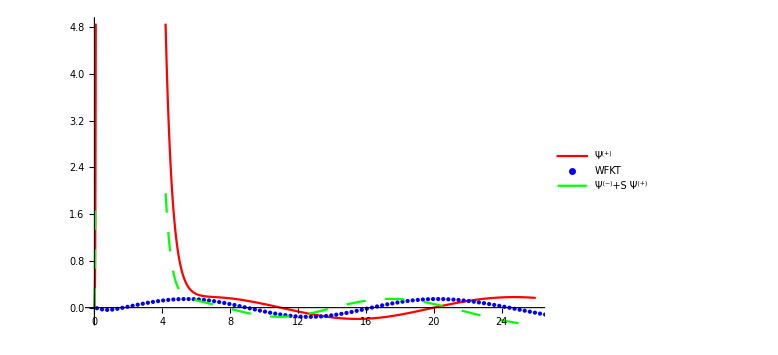

```mathematica
gwidths=ReadList["./WIDTHS",Real,aw];
uecoeffpsip=ReadList["./UECO_PSIPM",{Real,Real},aw];
hpm=ReadList["./UECO_FREE",{Real,Real,Real,Real},aw];
wefu=ReadList["./WELFU",Real,RecordLists->True];
(* <r|Ψ^+> = r Subscript[Σc, i] e^(-γ/2 r^2) *)
psip[r_]:=Sum[r (uecoeffpsip[[i]][[1]]+I uecoeffpsip[[i]][[2]]) Exp[-gwidths[[i]]/2 r^2],{i,1,aw}];
hpl[r_]:=Sum[r (hpm[[i]][[1]]+I hpm[[i]][[2]]) Exp[-gwidths[[i]]/2 r^2],{i,1,aw}];
hmi[r_]:=Sum[r (hpm[[i]][[3]]+I hpm[[i]][[4]]) Exp[-gwidths[[i]]/2 r^2],{i,1,aw}];
wfkt=Table[{wefu[[i]][[1]],wefu[[i]][[2]]+I wefu[[i]][[3]]},{i,1,100}];
Show[
Plot[Re[psip[x]],{x,0,26},PlotStyle->{RGBColor[1,0,0]},PlotRange->Automatic,PlotLegends->{"Ψ^(+)"},ImageSize->Large],
ListPlot[Re[wfkt],PlotStyle->{Blue,PointSize->0.005},PlotLegends->{"WFKT"},ImageSize->Large],Plot[Re[I/2 (hmi[x]-sm hpl[x])],{x,0,26},PlotStyle->{Dashing[Large],Thick,Green,PointSize->0.01},PlotLegends->{"Ψ^(-)+S Ψ^(+)"},ImageSize->Large]]
```

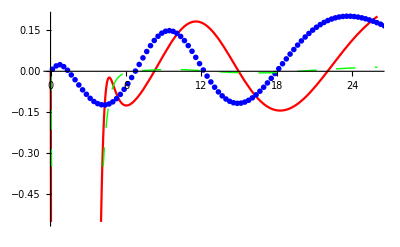

```mathematica
GraphicsGrid[
{{Show[
Plot[Re[psip[x]],{x,0,26},PlotStyle->{RGBColor[1,0,0]},PlotRange->Automatic,PlotLegends->"Ψ^(+)",ImageSize->Large],
ListPlot[Re[wfkt],PlotStyle->{Blue,PointSize->0.005},PlotLegends->"WFKT",ImageSize->Large],Plot[Re[I/2 (hmi[x]-sm hpl[x])],{x,0,26},PlotStyle->{Dashing[Large],Thick,Green,PointSize->0.01},PlotLegends->"Ψ^(-)+S Ψ^(+)",ImageSize->Large]],
Show[
Plot[Im[psip[x]],{x,0,26},PlotStyle->{RGBColor[1,0,0]}],
ListPlot[Im[wfkt],PlotStyle->{Blue,PointSize->0.01}],Plot[Im[I/2 (hmi[x]-sm hpl[x])],{x,0,26},PlotStyle->{Dashing[Large],Thick,Green,PointSize->0.01}]]}}
]
```

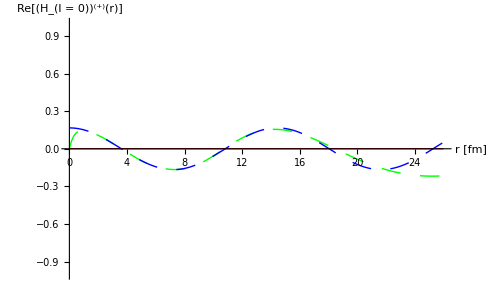

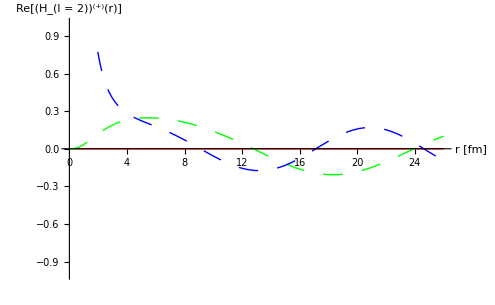

```mathematica
gwidths=ReadList["~/Kette/IN_FILES/d/global_lec/WIDTHS",Real,20];
uecoeffcoul=ReadList["~/Kette/IN_FILES/d/global_lec/UECO_COUL",{Real,Real,Real,Real}];
couls[r_]:=Sum[(uecoeffcoul[[i]][[1]]+I uecoeffcoul[[i]][[2]]) Exp[-gwidths[[i]]/2 r^2],{i,1,20}];
could[r_]:=Sum[(uecoeffcoul[[i+20]][[1]]+I uecoeffcoul[[i+20]][[2]]) Exp[-gwidths[[i]]/2 r^2],{i,1,20}];
pm=1;
ll=0;
Show[Plot[wefnor Re[Sqrt[0.5 Pi k x] ((-1)^ll BesselJ[-0.5-ll,k x](-1)^(pm)I BesselJ[0.5+ll,k x])],{x,0,26},PlotStyle->{RGBColor[1,0,0]},AxesLabel->{"r [fm]","Re[(H_(l = 0))^(+)(r)]"}],Plot[Re[x^(ll+1) couls[x]],{x,0,26},PlotStyle->{Green,Dashing[Large],Thick}],Plot[wefnor Re[I Sqrt[0.5 Pi k x] Exp[I Pi ll] HankelH1[0.5+ll,k x]],{x,0,26},PlotStyle->{Blue,Dashing[Large],Thick}]]
ll=2;
Show[Plot[wefnor Re[Sqrt[0.5 Pi k x] ((-1)^ll BesselJ[-0.5-ll,k x](-1)^(pm)I BesselJ[0.5+ll,k x])],{x,0,26},PlotStyle->{RGBColor[1,0,0]},AxesLabel->{"r [fm]","Re[(H_(l = 2))^(+)(r)]"}],Plot[Re[x^(ll+1) could[x]],{x,0,26},PlotStyle->{Green,Dashing[Large],Thick}],Plot[wefnor Re[I Sqrt[0.5 Pi k x] Exp[I Pi ll] HankelH1[0.5+ll,k x]],{x,0,26},PlotStyle->{Blue,Dashing[Large],Thick}]]
```

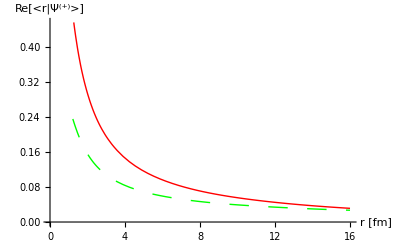

```mathematica
gwidths=ReadList["~/Kette/IN_FILES/d/global_lec/WIDTHS",Real,20];
uecoefffree=ReadList["~/Kette/IN_FILES/d/DWBA_TEST-neu/UECO_COUL",{Real,Real,Real,Real}];
uecoeffp=ReadList["~/Kette/IN_FILES/d/DWBA_TEST-neu/UECO_P",{Real,Real}];
free[r_]:=Sum[(uecoefffree[[i]][[1]]+I uecoefffree[[i]][[2]]) Exp[-gwidths[[i]]/2 r^2],{i,1,20}];
psip[r_]:=Sum[(uecoeffp[[i]][[1]]+I uecoeffp[[i]][[2]]) Exp[-gwidths[[i]]/2 r^2],{i,1,20}];
Show[Plot[Re[free[x]],{x,0,16},PlotStyle->{RGBColor[1,0,0]},AxesLabel->{"r [fm]","Re[<r|Ψ^(+)>]"}],Plot[Re[psip[x]],{x,0,16},PlotStyle->{Green,Dashing[Large],Thick}]]
```

```mathematica
wefnor^2 Sum[Sum[Sqrt[Pi/2] (uecoefffree[[i]][[1]]-I uecoefffree[[i]][[2]]) (uecoeffp[[i]][[1]]+I uecoeffp[[i]][[2]]) (gwidths[[i]]+gwidths[[j]])^(-3/2),{j,1,20}],{i,1,20}]
```

17.6729-7.09159 ⅈ

# d-bound state

- u_nl(r)=r^(l+1)e^(-γ_n r^2)

1, Calc bis S_POLE mit Kette (IWEFU=3, IPLO=1)
2, copy CWF aus OUTPUTSPOLE nach UECO und Weiten aus INQUA nach WIDTHS
3, copy Wfkt. aus OUTPUTSPOLE nach WEFU_<E> fuer gnuplot

```mathematica
aw=20;
```

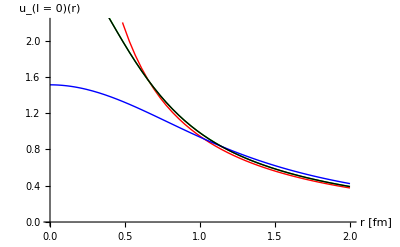

```mathematica
gwidthsa=ReadList["~/Kette/IN_FILES/d/global_lec/WIDTHS-120",Real,aw];
gwidthsb=ReadList["~/Kette/IN_FILES/d/global_lec/WIDTHS-12",Real,aw];
uecoeffpsipa=ReadList["~/Kette/IN_FILES/d/global_lec/bdg/OUTPUT-1600",Real,aw];
uecoeffpsipb=ReadList["~/Kette/IN_FILES/d/global_lec/bdg/OUTPUT-800",Real,aw];
uecoeffpsipc=ReadList["~/Kette/IN_FILES/d/global_lec/bdg/OUTPUT-400",Real,aw];
uecoeffpsipaa=ReadList["~/Kette/IN_FILES/d/global_lec/bdg/OUTPUT-1600-12",Real,aw];
uecoeffpsipbb=ReadList["~/Kette/IN_FILES/d/global_lec/bdg/OUTPUT-800-12",Real,aw];
uecoeffpsipcc=ReadList["~/Kette/IN_FILES/d/global_lec/bdg/OUTPUT-400-12",Real,aw];
(* <r|d> = r Subscript[Σc, i] e^(-γ/2 r^2) *)
ub=2;
l=-1;
dwea[r_]:=Sum[r^(l+1) (uecoeffpsipa[[i]]) Exp[-gwidthsa[[i]]/2 r^2],{i,1,aw}];
dweb[r_]:=Sum[r^(l+1) (uecoeffpsipb[[i]]) Exp[-gwidthsa[[i]]/2 r^2],{i,1,aw}];
dwec[r_]:=Sum[r^(l+1) (uecoeffpsipc[[i]]) Exp[-gwidthsa[[i]]/2 r^2],{i,1,aw}];
dweaa[r_]:=Sum[r^(l+1) (uecoeffpsipaa[[i]]) Exp[-gwidthsb[[i]]/2 r^2],{i,1,aw}];
dwebb[r_]:=Sum[r^(l+1) (uecoeffpsipbb[[i]]) Exp[-gwidthsb[[i]]/2 r^2],{i,1,aw}];
dwecc[r_]:=Sum[r^(l+1) (uecoeffpsipcc[[i]]) Exp[-gwidthsb[[i]]/2 r^2],{i,1,aw}];
Show[Plot[dwea[x],{x,0,ub},PlotStyle->{RGBColor[1,0,0]},AxesLabel->{"r [fm]","u_(l = 0)(r)"},PlotRange->{Automatic,{0,2.2}}],
Plot[dweb[x],{x,0,ub},PlotStyle->{RGBColor[0,1,0]}],Plot[dwec[x],{x,0,ub},PlotStyle->{RGBColor[0,0,1]}],
Plot[dweaa[x],{x,0,ub},PlotStyle->{Black}],Plot[dwebb[x],{x,0,ub},PlotStyle->{Black}],Plot[dwecc[x],{x,0,ub},PlotStyle->{Black}]]
```